```mathematica
Clear[tm,P,xinitial,yinitial,eqs,x,y,s]
```

```mathematica
(*轨道坐标*)
```

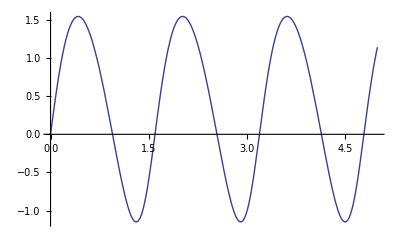

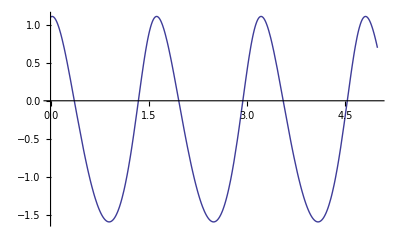

```mathematica
tm=5;P=4.0 π^2;
xinitial={0,6.5};yinitial={1.1,0.8};
eqs={x''[t]==-P*x[t]/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-P*y[t]/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[eqs,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
Plot[x[t],{t,0,tm}]
Plot[y[t],{t,0,tm}]
```

```mathematica
(*傅里叶级数分解*)
```

basic frequence=0.625976Hz

an | bn
0.593999 | 0
-0.343003 | 1.28388
0.0257235 | 0.147953
0.0144595 | 0.0209434
0.00439752 | 0.00260529
0.00112174 | 0.000116327
0.000250094 | -0.0000851561
0.0000467863 | -0.0000444585
6.02643×10^-6 | -0.0000151281
-2.13527×10^-7 | -4.22478×10^-6
-5.09694×10^-7 | -1.01548×10^-6
-2.32317×10^-7 | -2.17952×10^-7
-7.78194×10^-8 | -5.33733×10^-8
-2.17501×10^-8 | -2.85779×10^-8
-5.44385×10^-9 | -2.71751×10^-8
-1.50308×10^-9 | -2.69842×10^-8
-5.25835×10^-10 | -2.62301×10^-8
-4.44539×10^-10 | -2.5142×10^-8
-4.76386×10^-10 | -2.36913×10^-8

an | bn
-0.726566 | 0
1.29188 | 0.326627
0.147986 | -0.0271079
0.0208734 | -0.014622
0.00258416 | -0.00441663
0.000111376 | -0.00112334
-0.000086145 | -0.000249983
-0.0000445976 | -0.0000466881
-0.0000151089 | -6.00336×10^-6
-4.18444×10^-6 | 2.08051×10^-7
-9.76202×10^-7 | 4.97087×10^-7
-1.82094×10^-7 | 2.1882×10^-7
-2.07451×10^-8 | 6.51005×10^-8
1.81676×10^-9 | 1.01937×10^-8
1.26766×10^-9 | -5.30379×10^-9
-5.00951×10^-10 | -8.54731×10^-9
-1.28987×10^-9 | -8.81702×10^-9
-1.53129×10^-9 | -8.31843×10^-9
-1.3446×10^-9 | -7.71483×10^-9

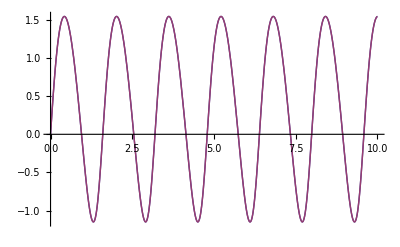

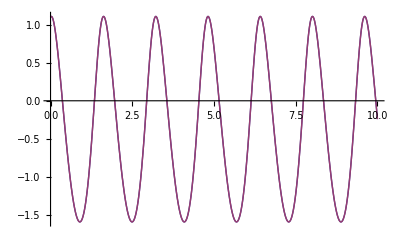

```mathematica
tm=10;P=4.0 π^2;
xinitial={0,6.5};yinitial={1.1,0.8};
eqs={x''[t]==-P*x[t]/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-P*y[t]/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[eqs,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
(*finding period and basic frequence*)
peak1=FindMaximum[x[t],{t,0.5}];
peak2=FindMaximum[x[t],{t,2}];
T=(t/.peak2[[2]])-(t/.peak1[[2]]);
Print["basic frequence=",1/T,"Hz"]
ω=2π/T;
(*finding harmonic coefficent*)
xcoef={{"an","bn"}};
ax0=2/T NIntegrate[x[t],{t,0,T}];
AppendTo[xcoef,{ax0,0}];
Do[a=2/T NIntegrate[x[t]Cos[j*ω*t],{t,0,T},AccuracyGoal->12];
b=2/T NIntegrate[x[t]Sin[j*ω*t],{t,0,T},AccuracyGoal->12];
AppendTo[xcoef,{a,b}],{j,1,18}]
ycoef={{"an","bn"}};
ay0=2/T NIntegrate[y[t],{t,0,T}];
AppendTo[ycoef,{ay0,0}];
Do[a=2/T NIntegrate[y[t]Cos[j*ω*t],{t,0,T},AccuracyGoal->12];
b=2/T NIntegrate[y[t]Sin[j*ω*t],{t,0,T},AccuracyGoal->12];
AppendTo[ycoef,{a,b}],{j,1,18}]
(*display coefficents*)
xcoef//TableForm
ycoef//TableForm
(*constructing function*)
fx=ax0/2+Sum[xcoef[[j,1]]*Cos[(j-2)ω*t]+xcoef[[j,2]]*Sin[(j-2)ω*t],{j,3,20}];
fy=ay0/2+Sum[ycoef[[j,1]]*Cos[(j-2)ω*t]+ycoef[[j,2]]*Sin[(j-2)ω*t],{j,3,20}];
(*comparing*)
Plot[{x[t],fx},{t,0,tm}]
Plot[{y[t],fy},{t,0,tm}]
```

```mathematica
Clear[tm,P,xinitial,yinitial,eqs,x,y,s,peak1,peak2,T,ω,xcoef,ycoef,ax0,ay0,a,b,fx,fy]
```

```mathematica
sam=5000
```

5000

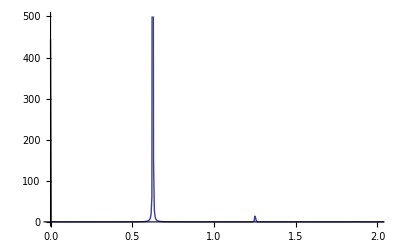

e:/orbitx.dat

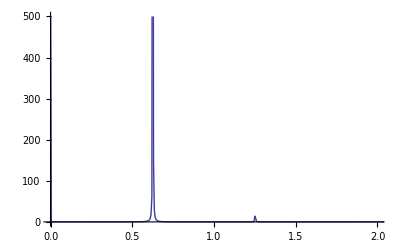

e:/orbity.dat

```mathematica
(*傅里叶变换分解*)
tm=200.0;P=4.0 π^2;
xinitial={0,6.5};yinitial={1.1,0.8};
eqs={x''[t]==-P*x[t]/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-P*y[t]/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[eqs,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
sam=5000;
signal=Table[x[t],{t,0,tm,tm/sam}];
ps=Abs[Fourier[signal]]^2;
len=Length[ps];
ps=Table[{(j-1)/tm,ps[[j]]},{j,1,len}];
ListLinePlot[ps,PlotRange->{{0,2},{0,500}}]
Export["e:/orbitx.dat",ps]
signal=Table[y[t],{t,0,tm,tm/sam}];
ps=Abs[Fourier[signal]]^2;
len=Length[ps];
ps=Table[{(j-1)/tm,ps[[j]]},{j,1,len}];
ListLinePlot[ps,PlotRange->{{0,2},{0,500}}]
Export["e:/orbity.dat",ps]
```

```mathematica
Clear[tm,P,xinitial,yinitial,eqs,x,y,s,sam,signal,ps,len]
```